```mathematica
(* set directory for image exports *)
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

/Users/gracezhang/Documents/GitHub/Oral_Exam_Paper

Saddle-node bifurcation.

```mathematica
plot1 = Show[StreamPlot[{1-x^2,-y},{x,-2,2},{y,-2,2},AxesLabel->{x,y} , FrameTicks->None, Background->RGBColor[1,1,1, 0.5]]];
plot2 = Show[StreamPlot[{0-x^2,-y},{x,-2,2},{y,-2,2},AxesLabel->{x,y} , FrameTicks->None, Background->RGBColor[1,1,1, 0.5]]];
plot3 = Show[StreamPlot[{-1-x^2,-y},{x,-2,2},{y,-2,2},AxesLabel->{x,y} , FrameTicks->None, Background->RGBColor[1,1,1, 0.5]]];
```

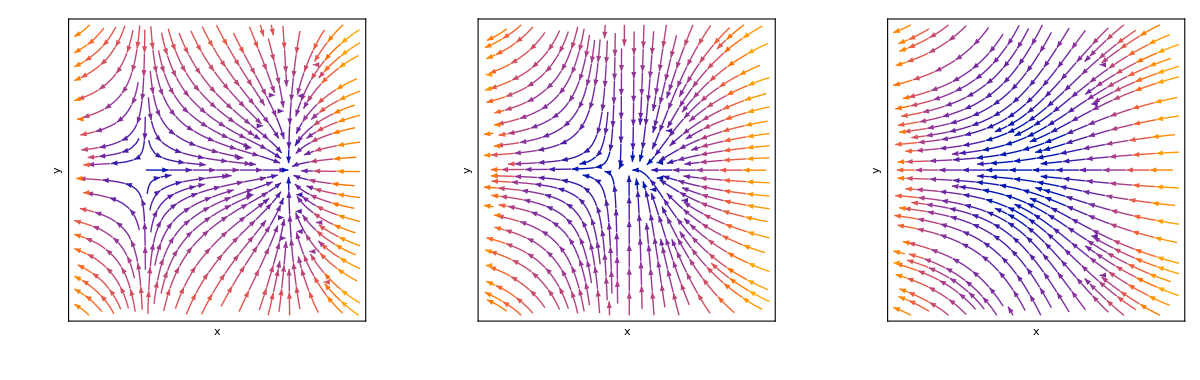

figs/saddle_node_bif_example.png

```mathematica
image= GraphicsRow[{plot1, plot2, plot3}]
Export["figs/saddle_node_bif_example.png", image, Background->None]
```